# Perceptual Metrics Demos & Examples

This notebook demonstrates using PerceptualMetrics.wl to calculate LPIPS, L2, DSSIM, and PSNR metrics.

## 1. Package Initialization & Session Startup

```mathematica
Off[General::shdw]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/fxpppr/GitHub/PerceptualMetrics

```mathematica
Get["PerceptualMetrics.wl"]
```

```mathematica
session=StartPerceptualSession[]
```

ExternalSessionObject[…]

```mathematica
PerceptualInfo[session]
```

<|status→ok,pytorch_version→2.13.0,device→mps,mps_available→True,cuda_available→False,metrics→{lpips,l2,dssim,psnr},nets→{alex,vgg,squeeze},versions→{0.1,0.0},colorspaces→{Lab,RGB}|>

## 2. Sample Images Setup

```mathematica
img1=Rasterize[Graphics[{Hue[0.6],Disk[]}],ImageSize->{128,128}];img2=Blur[img1,4];GraphicsRow[{img1,img2},ImageSize->Medium]
```

-Graphics-

## 3. Scalar Perceptual Metrics Comparison

```mathematica
Association["LPIPS (Alex)"->PerceptualDistance[session,img1,img2,"Net"->"alex"],"LPIPS (VGG)"->PerceptualDistance[session,img1,img2,"Net"->"vgg"],"LPIPS (Squeeze)"->PerceptualDistance[session,img1,img2,"Net"->"squeeze"],"L2 (Lab)"->PerceptualDistance[session,img1,img2,"Metric"->"l2","ColorSpace"->"Lab"],"DSSIM (Lab)"->PerceptualDistance[session,img1,img2,"Metric"->"dssim","ColorSpace"->"Lab"],"PSNR (dB)"->PerceptualDistance[session,img1,img2,"Metric"->"psnr"]]
```

/Users/fxpppr/GitHub/PerceptualMetrics/.venv/lib/python3.11/site-packages/torchvision/models/_utils.py:207: UserWarning: The parameter 'pretrained' is deprecated since 0.13 and may be removed in the future, please use 'weights' instead.

warnings.warn(

/Users/fxpppr/GitHub/PerceptualMetrics/.venv/lib/python3.11/site-packages/torchvision/models/_utils.py:222: UserWarning: Arguments other than a weight enum or `None` for 'weights' are deprecated since 0.13 and may be removed in the future. The current behavior is equivalent to passing `weights=AlexNet_Weights.IMAGENET1K_V1`. You can also use `weights=AlexNet_Weights.DEFAULT` to get the most up-to-date weights.

warnings.warn(msg)

/Users/fxpppr/GitHub/PerceptualMetrics/.venv/lib/python3.11/site-packages/torchvision/models/_utils.py:222: UserWarning: Arguments other than a weight enum or `None` for 'weights' are deprecated since 0.13 and may be removed in the future. The current behavior is equivalent to passing `weights=VGG16_Weights.IMAGENET1K_V1`. You can also use `weights=VGG16_Weights.DEFAULT` to get the most up-to-date weights.

warnings.warn(msg)

/Users/fxpppr/GitHub/PerceptualMetrics/.venv/lib/python3.11/site-packages/torchvision/models/_utils.py:222: UserWarning: Arguments other than a weight enum or `None` for 'weights' are deprecated since 0.13 and may be removed in the future. The current behavior is equivalent to passing `weights=SqueezeNet1_1_Weights.IMAGENET1K_V1`. You can also use `weights=SqueezeNet1_1_Weights.DEFAULT` to get the most up-to-date weights.

warnings.warn(msg)

<|LPIPS (Alex)→0.0774051,LPIPS (VGG)→0.104434,LPIPS (Squeeze)→0.0606037,L2 (Lab)→0.000591774,DSSIM (Lab)→0.0229522,PSNR (dB)→29.7954|>

## 4. Spatial Perceptual Distance Maps

/Users/fxpppr/GitHub/PerceptualMetrics/.venv/lib/python3.11/site-packages/torchvision/models/_utils.py:207: UserWarning: The parameter 'pretrained' is deprecated since 0.13 and may be removed in the future, please use 'weights' instead.

warnings.warn(

/Users/fxpppr/GitHub/PerceptualMetrics/.venv/lib/python3.11/site-packages/torchvision/models/_utils.py:222: UserWarning: Arguments other than a weight enum or `None` for 'weights' are deprecated since 0.13 and may be removed in the future. The current behavior is equivalent to passing `weights=AlexNet_Weights.IMAGENET1K_V1`. You can also use `weights=AlexNet_Weights.DEFAULT` to get the most up-to-date weights.

warnings.warn(msg)

/Users/fxpppr/GitHub/PerceptualMetrics/.venv/lib/python3.11/site-packages/torchvision/models/_utils.py:222: UserWarning: Arguments other than a weight enum or `None` for 'weights' are deprecated since 0.13 and may be removed in the future. The current behavior is equivalent to passing `weights=VGG16_Weights.IMAGENET1K_V1`. You can also use `weights=VGG16_Weights.DEFAULT` to get the most up-to-date weights.

warnings.warn(msg)

Colorize::nlut: Cannot generate a color lookup table. Check the ColorFunction and ColorRule options.

Colorize::interr: An internal error occurred: $Failed.

Colorize::nlut: Cannot generate a color lookup table. Check the ColorFunction and ColorRule options.

Colorize::interr: An internal error occurred: $Failed.

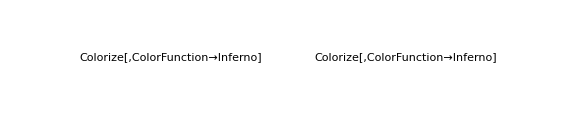

```mathematica
mapAlex=PerceptualSpatialMap[session,img1,img2,"Metric"->"lpips","Net"->"alex"];mapVGG=PerceptualSpatialMap[session,img1,img2,"Metric"->"lpips","Net"->"vgg"];GraphicsRow[{Colorize[mapAlex,ColorFunction->"Inferno"],Colorize[mapVGG,ColorFunction->"Inferno"]},ImageSize->Large]
```

## 5. Clean Up Session

```mathematica
StopPerceptualSession[session]
```